```mathematica
Statistical = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_2048_statistical_one_vp.csv"];
sorted = SortBy[Statistical,-#[[1]]&][[;;,1]];
```

```mathematica
sorted[[;;10]]
sorted[[-10;;]]
```

{2045.37,2038.44,2037.16,2036.62,2033.74,2029.5,2024.07,2021.74,2017.75,2016.61}

{1461.21,1461.1,1457.86,1456.25,1454.24,1453.18,1448.61,1448.36,1434.48,1430.99}

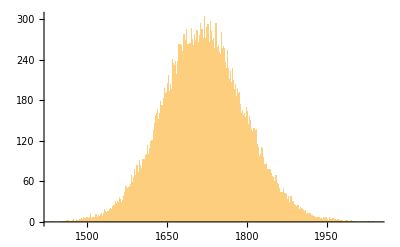

```mathematica
Histogram[Statistical[[;;,1]][[;;100000]],1000]
```

```mathematica
profs = {{6,6,6,6,6,6},{7,5,7,5,7,5},{8,4,8,4,8,4},{9,3,9,3,9,3},{10,2,10,2,10,2},{11,1,11,1,11,1}};
data = Table[Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_"<>StringReplace[ToString[prof],{"{"-> "[","}"-> "]"}]<>"_statistical_one_vp.csv"],{prof,profs}];
```

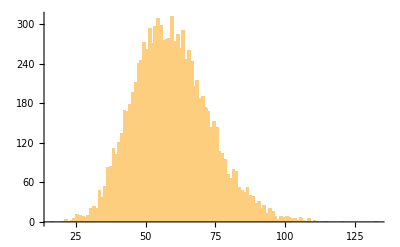
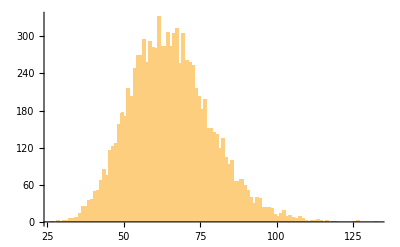
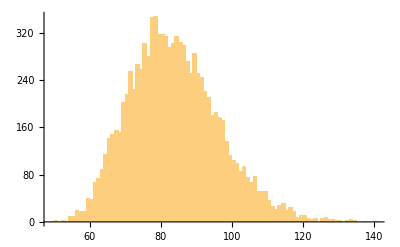
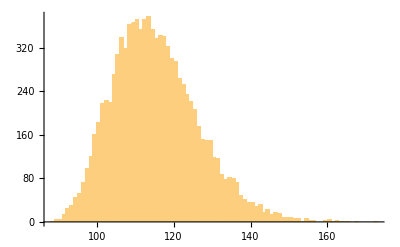
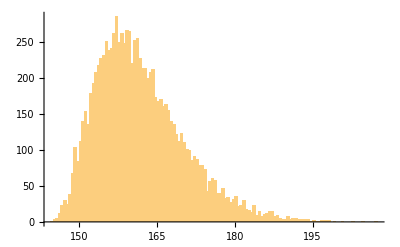
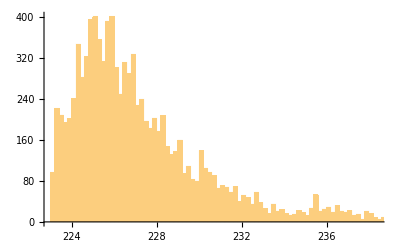

```mathematica
Table[Histogram[Flatten[d],100],{d,data}]
```

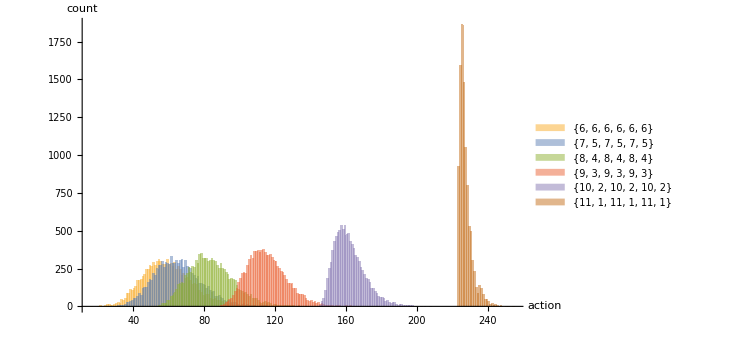

```mathematica
Histogram[data[[;;,;;,1]],300,ChartLegends->Table[ToString[p],{p,profs}],AxesLabel->{action,count}]
```